```mathematica
f[x_,y_]:=1/2(x^2+y^2)
```

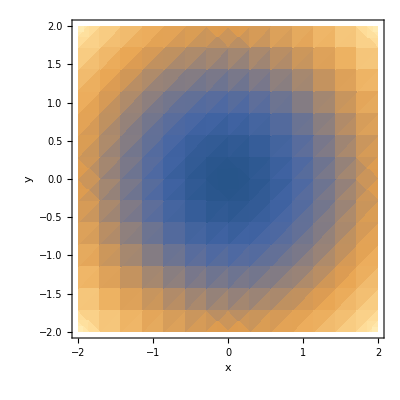

```mathematica
DensityPlot[f[x,y],{x,-2,2},{y,-2,2},AxesLabel->{x,y}]
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2},AxesLabel->{x,y,f}]
```

-Graphics3D-

```mathematica
gradF[x_,y_]={D[f[x,y],x],D[f[x,y],y]}
```

{x,y}

```mathematica
gradF[3,5]
```

{3,5}

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

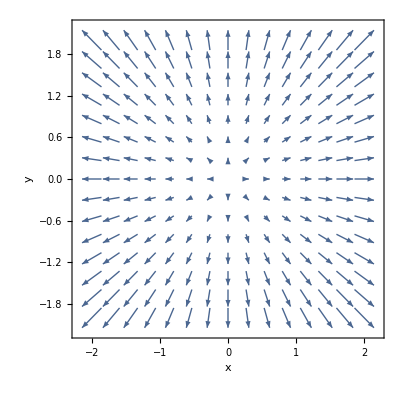

```mathematica
VectorPlot[gradF[x, y],{x,-2,2},{y,-2,2},AxesLabel->{x,y}]
```

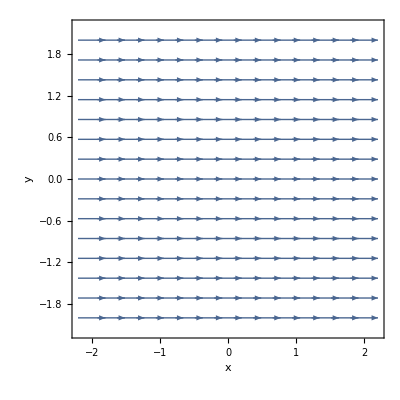

```mathematica
VectorPlot[{1,0},{x,-2,2},{y,-2,2},AxesLabel->{x,y}]
```